```mathematica
Clear["Global`*"]
```

```mathematica
P1={Cos[Ω1]Cos[ω1]-Sin[Ω1]Sin[ω1]Cos[i1],Sin[Ω1]Cos[ω1]+Cos[Ω1]Sin[ω1]Cos[i1],Sin[ω1]Sin[i1]}
Q1={-Cos[Ω1]Sin[ω1]-Sin[Ω1]Cos[ω1]Cos[i1],-Sin[Ω1]Sin[ω1]+Cos[Ω1]Cos[ω1]Cos[i1],Cos[ω1]Sin[i1]}
```

{Cos[ω1] Cos[Ω1]-Cos[i1] Sin[ω1] Sin[Ω1],Cos[i1] Cos[Ω1] Sin[ω1]+Cos[ω1] Sin[Ω1],Sin[i1] Sin[ω1]}

{-Cos[Ω1] Sin[ω1]-Cos[i1] Cos[ω1] Sin[Ω1],Cos[i1] Cos[ω1] Cos[Ω1]-Sin[ω1] Sin[Ω1],Cos[ω1] Sin[i1]}

```mathematica
a1=6678137/6378140;e1=0.1;i1=45°;Ω1=45°;ω1=45°;E1=0;μ=1;
```

```mathematica
r1[0]=N[a1(Cos[E1]-e1)*P1+a1 √(1-e1^2)Sin[E1]*Q1]
```

{0.138001,0.80433,0.471166}

```mathematica
r1'[0]=N[(√(μ a1))/(√((r1[0][[1]])^2+(r1[0][[2]])^2+(r1[0][[3]])^2))(-Sin[E1]P1+√(1-e1^2)Cos[E1]Q1)]
```

{-0.9222,-0.158225,0.540212}

```mathematica
eq1={x1''[t]==-μ/((√(x1[t]^2+y1[t]^2+z1[t]^2))^3)x1[t],y1''[t]==-μ/((√(x1[t]^2+y1[t]^2+z1[t]^2))^3)y1[t],z1''[t]==-μ/((√(x1[t]^2+y1[t]^2+z1[t]^2))^3)z1[t]}
```

{x1''[t]==-x1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2)),y1''[t]==-y1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2)),z1''[t]==-z1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2))}

```mathematica
eq2={x1[0]==r1[0][[1]],y1[0]==r1[0][[2]],z1[0]==r1[0][[3]]}
```

{x1[0]==0.138001,y1[0]==0.80433,z1[0]==0.471166}

```mathematica
eq3={x1'[0]==r1'[0][[1]],y1'[0]==r1'[0][[2]],z1'[0]==r1'[0][[3]]}
```

{x1'[0]==-0.9222,y1'[0]==-0.158225,z1'[0]==0.540212}

```mathematica
sol1=NDSolve[Flatten[{eq1,eq2,eq3}],{x1[t],y1[t],z1[t],x1'[t],y1'[t],z1'[t]},{t,0,1000},MaxSteps->100000,Method->"ImplicitRungeKutta"]
```

{{x1[t]→InterpolatingFunction[{{0.,1000.}},<>][t],y1[t]→InterpolatingFunction[{{0.,1000.}},<>][t],z1[t]→InterpolatingFunction[{{0.,1000.}},<>][t],x1'[t]→InterpolatingFunction[{{0.,1000.}},<>][t],y1'[t]→InterpolatingFunction[{{0.,1000.}},<>][t],z1'[t]→InterpolatingFunction[{{0.,1000.}},<>][t]}}

```mathematica
plot1=ParametricPlot3D[Flatten[Evaluate[{x1[t],y1[t],z1[t]}/.sol1]],{t,0,1000},AspectRatio->1,BoxRatios->1,AxesLabel->{"x","y","z"},PlotLabel->"偏心率为0.1时的轨道",AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},PlotStyle->RGBColor[1,0,0]]
```

-Graphics3D-

```mathematica
a2=6678137/6378140;e2=0.0001;i2=45°;Ω2=45°;ω2=45°;E2=0;μ=1;
```

```mathematica
P2={Cos[Ω2]Cos[ω2]-Sin[Ω2]Sin[ω2]Cos[i2],Sin[Ω2]Cos[ω2]+Cos[Ω2]Sin[ω2]Cos[i2],Sin[ω2]Sin[i2]};
Q2={-Cos[Ω2]Sin[ω2]-Sin[Ω2]Cos[ω2]Cos[i2],-Sin[Ω2]Sin[ω2]+Cos[Ω2]Cos[ω2]Cos[i2],Cos[ω2]Sin[i2]};
```

```mathematica
r2[0]=N[a2(Cos[E2]-e2)*P2+a2 √(1-e2^2)Sin[E2]*Q2]
```

{0.153319,0.893611,0.523465}

```mathematica
r2'[0]=N[(√(μ a2))/(√((r2[0][[1]])^2+(r2[0][[2]])^2+(r2[0][[2]])^2))(-Sin[E2]P2+√(1-e2^2)Cos[E2]Q2)]
```

{-0.68608,-0.117713,0.401897}

```mathematica
eq4={x2''[t]==-μ/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2))x2[t],y2''[t]==-μ/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2))y2[t],z2''[t]==-μ/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2))z2[t]}
```

{x2''[t]==-x2[t]/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2)),y2''[t]==-y2[t]/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2)),z2''[t]==-z2[t]/((x2[t]^2+y2[t]^2+z2[t]^2)^(3/2))}

```mathematica
eq5={x2[0]==r2[0][[1]],y2[0]==r2[0][[2]],z2[0]==r2[0][[3]]}
```

{x2[0]==0.153319,y2[0]==0.893611,z2[0]==0.523465}

```mathematica
eq6={x2'[0]==r2'[0][[1]],y2'[0]==r2'[0][[2]],z2'[0]==r2'[0][[3]]}
```

{x2'[0]==-0.68608,y2'[0]==-0.117713,z2'[0]==0.401897}

```mathematica
sol2=NDSolve[Flatten[{eq4,eq5,eq6}],{x2[t],y2[t],z2[t],x2'[t],y2'[t],z2'[t]},{t,0,1000},MaxSteps->100000,Method->"ImplicitRungeKutta"];
```

```mathematica
plot2=ParametricPlot3D[Evaluate[{x2[t],y2[t],z2[t]}/.sol2],{t,0,1000},AspectRatio->1,BoxRatios->1,AxesLabel->{"x","y","z"},PlotLabel->"偏心率为0.0001时的轨道",AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},PlotStyle->RGBColor[0,0,1]]
```

-Graphics3D-

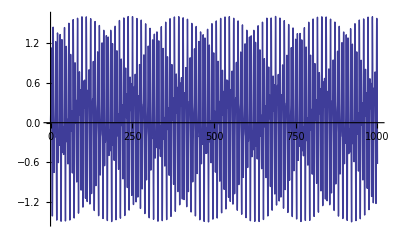

```mathematica
Plot[Evaluate[x2[t]/.sol2]-Evaluate[x1[t]/.sol1],{t,0,1000}]
```

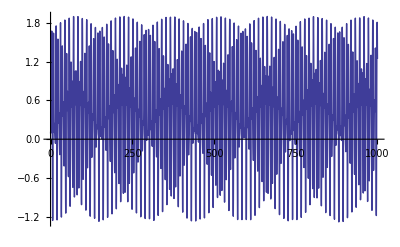

```mathematica
Plot[Evaluate[y2[t]/.sol2]-Evaluate[y1[t]/.sol1],{t,0,1000}]
```

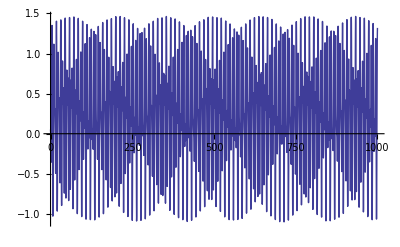

```mathematica
Plot[Evaluate[z2[t]/.sol2]-Evaluate[z1[t]/.sol1],{t,0,1000}]
```

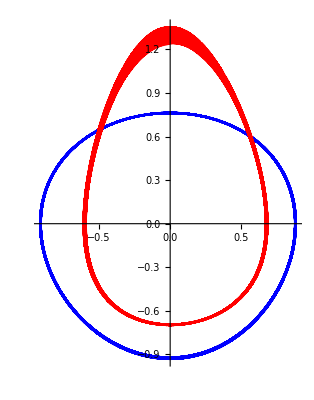

```mathematica
ParametricPlot[{Evaluate[{x1[t],x1'[t]}/.sol1],Evaluate[{x2[t],x2'[t]}/.sol2]},{t,0,1000},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]
```

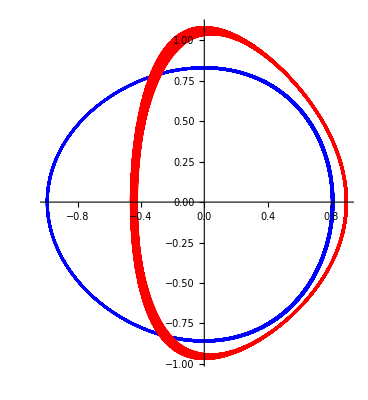

```mathematica
ParametricPlot[{Evaluate[{y1[t],y1'[t]}/.sol1],Evaluate[{y2[t],y2'[t]}/.sol2]},{t,0,1000},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]
```

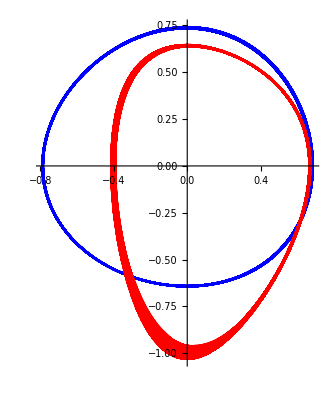

```mathematica
ParametricPlot[{Evaluate[{z1[t],z1'[t]}/.sol1],Evaluate[{z2[t],z2'[t]}/.sol2]},{t,0,1000},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]
```

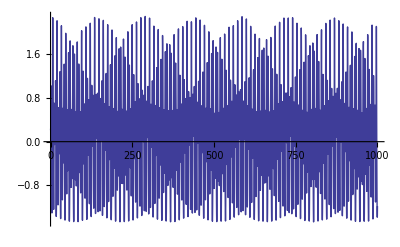

```mathematica
Plot[Evaluate[x2'[t]/.sol2]-Evaluate[x1'[t]/.sol1],{t,0,1000}]
```

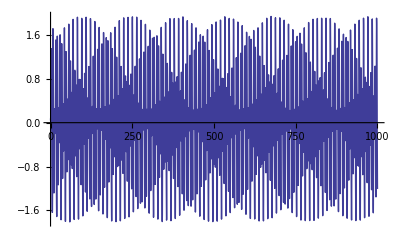

```mathematica
Plot[Evaluate[y2'[t]/.sol2]-Evaluate[y1'[t]/.sol1],{t,0,1000}]
```

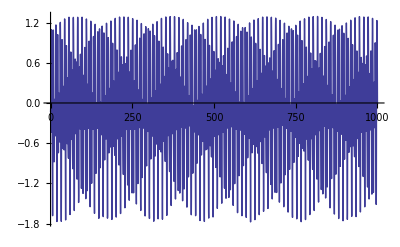

```mathematica
Plot[Evaluate[z2'[t]/.sol2]-Evaluate[z1'[t]/.sol1],{t,0,1000}]
```

```mathematica
DSolve[Flatten[{eq1,eq2,eq3}],{x1[t],y1[t],z1[t]},t]
```

DSolve[{x1''[t]==-x1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2)),y1''[t]==-y1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2)),z1''[t]==-z1[t]/((x1[t]^2+y1[t]^2+z1[t]^2)^(3/2)),x1[0]==0.138001,y1[0]==0.80433,z1[0]==0.471166,x1'[0]==-0.9222,y1'[0]==-0.158225,z1'[0]==0.540212},{x1[t],y1[t],z1[t]},t]

```mathematica
√((r1[0][[1]])^2+(r1[0][[2]])^2+(r1[0][[3]])^2)
```

0.942332

```mathematica
Norm[r2[0]]
```

1.04693